# Report Project I

Course code: IX1500
Date: 2018-09-14

Michel Ouadria, ouadria@kth.se
Rikard Jakobsson, rikjak@kth.se

Task 1: Probability Experiment

## Summary

### Task

Assume that you play a variant of a poker game with five cards that is using a subset of two ordinary deck of cards. The subset considered is cards valued 9,10,J,Q,K,A from the two decks, in total 48 cards.

Calculate the exact probability of the following hands using the  census method.

If a given hand contains different valued hands only one (the highest rank) is considered.

One pair

Two pairs

Three of a kind

Four of a kind

Five of a kind

Full hand

Straight

Flush

Straight flush

Nothing

### Result

●Straight Flush:
	• 256
	• 0.0149506%

●Straight:
	• 65 280
	• 3.81241%

●Full House:
	• 47 040
	• 2.74718%
	
●Five of a kind:
	• 336
	• 0.0196227%
	
●Four of a kind:
	• 16 800
	• 0.981134%
	
●Flush:
	• 2912
	• 0.170063%
	
●Three of a kind:
	• 215 040
	• 12.5585%
	
●Two pairs:
	• 37 5840
	• 21.9494%
	
●One pair:
	• 85 8240
	• 50.1219%
	
●Nothing:
	 • 130 560
	 •7.62481%

### Discussion

For this discussion we assume the reader knows the probabilities for getting hands in a standard poker game.
In this variant of poker there is an increased chance of getting a point giving hand since there is a much smaller spread in the value of the cards (6 values compared to 14 values), as well as having a lot more duplicates due to mixing two decks of cards. We can see this clearly if we look at the probabilities calculated in this project and the probabilities from a standard take 5 poker game. 

Ours had a higher probability for all hands except flush, which is explained by it being covered by other hands. The best example of this is the four of a kind. In regular poker it is a very rare hand, since there are only four of each value, but in this game we get a probability about 40 times greater than that. 
●Straight Flush:
	The probability of getting a straight flush is about 10 times greater than usual. This is because we have duplicates of each suite and there are fewer values to choose from.

●Straight:
	 The probability of getting a straight is a bit less than 10 times greater than usual. This is because there are fewer values to choose from.

●Full House:
	 Getting a Full house is about 19 times more likely. This is because there is a much greater chance of getting pairs and threes
	 
	
●Five of a kind:
This is about an infinite amount more probable because it is impossible to get in regular poker.
	
●Four of a kind:
This is the hand that has seen the highest increase compared to the regular game. There is as mentioned about 40 times more likely since there are many more cards to choose from.	
●Flush:
This is the only point giving hand that has seen a decrease compared to regular poker. This is due to the fact that it will be outranked by more hands and therefor a lot of flushes will be covered by other more valuable hands.
	
●Three of a kind:
This is about 6 times more likely than usual. This is due to the fact that there are 8 of each value instead of 4.
	
●Two pairs:
This is about 5 times more likely than usual. This is as in most cases due to the fact that we have more cards of each value and there are fewer values to choose from. 
	
●One pair:
This is the hand that has seen the smallest increase. This is for the same reason as the flush mentioned above, ie a lot of hands containing a pair also contains something else to make it more valuable.
	
●Nothing:
This is a lot less common due to the fact that the possibility of a point giving hand is much higher.
For this discussion we assume the reader knows the probabilities for getting hands in a standard poker game.

## Code

```mathematica
deck = {109,109,110,110,111,111,112,112,113,113,114,114,209,209,210,210,211,211,212,212,213,213,214,214,309, 309,310,310,311,
311,312,312,313,313,314,314,409,409,410,410,411,411,412,412,
413,413,414,414};

hand = Subsets[deck,{5}](*Sort deck with all subsets containing 5*)
sizeOfPermutations = Length[hand] (*Amount of different possible hands*)
```

{{109,109,110,110,111},{109,109,110,110,111},{109,109,110,110,112},{109,109,110,110,112},{109,109,110,110,113},{109,109,110,110,113},{109,109,110,110,114},{109,109,110,110,114},{109,109,110,110,209},{109,109,110,110,209},{109,109,110,110,210},{109,109,110,110,210},{109,109,110,110,211},{109,109,110,110,211},{109,109,110,110,212},{109,109,110,110,212},{109,109,110,110,213},{109,109,110,110,213},{109,109,110,110,214},{109,109,110,110,214},{109,109,110,110,309},{109,109,110,110,309},{109,109,110,110,310},{109,109,110,110,310},1712257,{411,412,413,414,414},{411,413,413,414,414},{411,412,412,413,413},{411,412,412,413,414},{411,412,412,413,414},{411,412,412,413,414},{411,412,412,413,414},{411,412,412,414,414},{411,412,413,413,414},{411,412,413,413,414},{411,412,413,414,414},{411,412,413,414,414},{411,412,413,413,414},{411,412,413,413,414},{411,412,413,414,414},{411,412,413,414,414},{411,413,413,414,414},{412,412,413,413,414},{412,412,413,413,414},{412,412,413,414,414},{412,412,413,414,414},{412,413,413,414,414},{412,413,413,414,414}}
 |  |  |  |

1712304

#### Straight flush

```mathematica
straightFlushQ[h_]:=MatchQ[h-h[[1]],{0,1,2,3,4}](*subtracts the first value from the rest and then checks if they are in ascending order*)
straightFlush =Count[hand, _?(straightFlushQ)]
N[straightFlush/sizeOfPermutations]*100
```

256

0.0149506

#### Straight

```mathematica
straightQ[{9,10,11,12,13}]:=True;(*All possible hands from 9 to K = True*)
straightQ[{10,11,12,13,14}]:=True;(*All possible hands from 10 to A = True *)
straightQ[{___}]:=False(*All other possibilities = False*)
straightRemoveSuiteQ[hand_]:= straightQ[Sort[Mod[hand,100]]]; (*Calculating suites by removing the first digit from all cards in the deck, i.e 109 = 9 ...*)
straight =(Count[hand,_?(straightRemoveSuiteQ)]-straightFlush) (*Final result of all the chances of getting straight. Subtract Straight flush since the cases above doesn't exclude it as a possibility*)
N[(straight)/sizeOfPermutations]*100 (*Probability*)
```

65280

3.81241

#### Full house

```mathematica
fullHouseQ[{x_,x_,x_,y_,y_}/;x≠y]:=True;(*Check for three of a kind and a pair, they can't be the same rank*)
fullHouseQ[{x_,x_,y_,y_,y_}/;x≠y]:=True;(*Second scenario*)
fullHouseQ[___]:=False;(*Everything else is excluded*)
fullHouseRemoveSuiteQ[hand_]:=fullHouseQ[Sort[Mod[hand,100]]]
fullHouse =Count[hand,_?(fullHouseRemoveSuiteQ)]
N[fullHouse/sizeOfPermutations]*100
```

47040

2.74718

#### Five of a kind

```mathematica
fiveOfAKindQ[{x_,x_,x_,x_,x_}]:=True;(*Check for five of a kind*)
fiveOfAKindQ[{___}]:=False;(*Exclude everything else*)
fiveOfAKindRemoveSuiteQ[hand_]:=fiveOfAKindQ[Sort[Mod[hand,100]]]
fioak = Count[hand,_?(fiveOfAKindRemoveSuiteQ)]
N[fioak/sizeOfPermutations]*100
```

336

0.0196227

#### Four of a kind

```mathematica
fourOfAKindQ[{x_,x_,x_,x_,y_}/;x≠y]:=True; (*Checks for four of a kind*)
fourOfAKindQ[{y_,x_,x_,x_,x_}/;x≠y]:=True; 
fourOfAKindQ[{___}]:=False;
fourOfAKindRemoveSuiteQ[hand_]:=fourOfAKindQ[Sort[Mod[hand,100]]];
foak = Count[hand,_?(fourOfAKindRemoveSuiteQ)]
N[foak/sizeOfPermutations]*100
```

16800

0.981134

#### Flush

```mathematica
flushQ[h_]:=MatchQ[(h-h[[1] ]),{0,0,0,0,0}](*Removes the value and only keeps the suit. Makes sure that all have the same suite by removeing the suite from the first one and checking if  htey are all zeor*)
flushGetSuiteQ[hand_]:= flushQ[Quotient[hand,100]](*Get the suite through quotienet function. I.e 109 = 1*)
flush=Count[hand,_?(flushGetSuiteQ)]- straightFlush
N[flush/sizeOfPermutations]*100
```

2912

0.170063

#### Three of a kind

```mathematica
threeOfAKindQ[{___,x_,x_,x_,x_,___}]:=False; (*Four of a kind excluded*)
threeOfAKindQ[{x_,x_,y_,y_,y_}/;x≠y]:=False;(*Full house excluded*)
threeOfAKindQ[{x_,x_,x_,y_,y_}/;x≠y]:=False;(*Second scenario of full house*)
threeOfAKindQ[{___,x_,x_,x_,___}]:=True; (*Three of a kind*)
threeOfAKindQ[{___}]:=False; 
threeOfAKindRemoveSuiteQ[hand_]:=threeOfAKindQ[Sort[Mod[hand,100]]];
threePair =Count[hand,_?(threeOfAKindRemoveSuiteQ)]
N[threePair/sizeOfPermutations]*100
```

215040

12.5585

#### Two Pair Flush

```mathematica
twoPairQ[{x_,x_,y_,y_,z_}/;x≠y≠z]:=True;(*Two pair*)
twoPairQ[{z_,x_,x_,y_,y_}/;x≠y≠z]:=True;(*Second scenario*)
twoPairQ[{x_,x_,z_,y_,y_}/;x≠y≠z]:=True;(*Third senario*)
twoPairQ[{___}]:=False;
twoPairRemoveSuiteQ[hand_]:=twoPairQ[Sort[Mod[hand,100]]];
(*Check when a hand with two pair without suite are the same as the flush suite*)
twoPairWithFlushQ[hand_]:=twoPairRemoveSuiteQ[hand]&&flushGetSuiteQ[hand]
twoPairwithFlush = Count[hand,_?(twoPairWithFlushQ)]
```

480

#### Two pair

```mathematica
(*Go through all possible cases of twoPair excl. suite and exclude cases where two pair are of the same suite*)
twoPair = Count[hand,_?(twoPairRemoveSuiteQ)]-twoPairwithFlush

N[twoPair/sizeOfPermutations]*100
```

375840

21.9494

#### One pair

```mathematica
pairQ[{x_,x_,y_,z_,w_}/;x≠y≠z≠w]:=True;(* First case of two pairs *)
pairQ[{y_,x_,x_,z_,w_}/;x≠y≠z≠w]:=True;(*Second case*)
pairQ[{y_,z_,x_,x_,w_}/;x≠y≠z≠w]:=True;(*Third case*)
pairQ[{y_,z_,w_,x_,x_}/;x≠y≠z≠w]:=True;(*Fourth case*)
pairQ[{___}]:=False (* else *)

pairRemoveSuiteQ[hand_]:=pairQ[Sort[Mod[hand,100]]]
pairWithFlushQ[hand_]:=pairRemoveSuiteQ[hand]&&flushGetSuiteQ[hand]
pairWithFlush = Count[hand,_?(pairWithFlushQ)];
onePair = Count[hand,_?(pairRemoveSuiteQ)]-pairWithFlush
N[onePair/sizeOfPermutations]*100
```

858240

50.1219

#### Nothing

```mathematica
noHand = Length[hand] -straightFlush - straight-flush-fullHouse-foak-threePair-fioak-twoPair-onePair
N[noHand/sizeOfPermutations]*100
```

130560

7.62481

Task 2: Combinatorial Calculus & Monte Carlo Experiment

## Summary

### Task

Consider the following C of the probability of getting four of a kind. In this case we are dealing with sampling without replacement and without regard to order. First choose one of six possibilities {9,…,A} to be the kind value x, then we choose four out of the eight x and finally we add a last card from the remaining 40. The multiplication principle gives the result.

### Result

Straight Flush:  2^5 Binomial[2, 1] Binomial[4, 1] = 256
Probability: 0.0149506%

Straight: Binomial[2, 1] Binomial[8, 1]^5- Straight Flush = 65 280
Probability: 3.81241%

Full House: Binomial[6, 1] Binomial[8, 3]Binomial[5, 1]Binomial[8, 2] = 47 040
Probability: 2.74718%

Flush: Binomial[12, 5] Binomial[4, 1] - Straight Flush = 2912
Probability: 0.170063%

Four of a kind: Binomial[6, 1] Binomial[8, 4]Binomial[40, 1] = 16 800
Probability: 0.981134%

Three of a kind: Binomial[6, 1] Binomial[8, 3]Binomial[5, 2]Binomial[8, 1]^2 = 215 040
Probability: 12.5585%

The result from the combinatorial calculations verifies the same probability as the census method.

## Code

### Deck

```mathematica
deckC=Binomial[48, 5]
```

1712304

### Straight Flush

The straight flush can start with possible cards, nine or ten, and can be of four possible suites. There are 2 choices for each spot.

```mathematica
straightFlushC=2^5 Binomial[2, 1] Binomial[4, 1]
```

256

```mathematica
N[(2^5 Binomial[2, 1] Binomial[4, 1])/deckC]*100
```

0.0149506

### Straight

The straight applies same principle above with the exception of flush, no sequence of five suites. 
Binomial[2, 1] = Two possible starting cards, pick one. Binomial[8, 1]=Eight possible values, including recurrence of same suite, pick one. Repeat five times. Exclude the possibility of flush and straight appearing together.

```mathematica
straightC=Binomial[2, 1] Binomial[8, 1]^5;
straightC - straightFlushC
```

```mathematica
N[(Binomial[2, 1] Binomial[8, 1]^5-2^5 Binomial[2, 1] Binomial[4, 1])/deckC]*100
```

3.81241

### Full House

The full house consists of three of kind and a pair of two in the same hand.
Binomial[6, 1]=Pick one out of six possible ranks.Binomial[8, 3]=Pick three out of eight possible values, including recurrence of same suite.Binomial[5, 1]=Pick one out of the remaining five cards.Binomial[8, 2]=Pick two out of eight possible suites, including recurrence of same suite.

```mathematica
fullHouseC=Binomial[6, 1] Binomial[8, 3]Binomial[5, 1]Binomial[8, 2]
```

47040

```mathematica
N[(Binomial[6, 1] Binomial[8, 3]Binomial[5, 1]Binomial[8, 2])/deckC]*100
```

2.74718

### Flush

The flush consists of a hand with hand of where all cards holds same suite, but not pair or straight of the rank.
Binomial[12, 5]=Pick five out of the 12 possible cards in a suiteBinomial[4, 1]=Pick a suite. Exclude all straight flushes.

```mathematica
flushC=Binomial[12, 5] Binomial[4, 1] ;
flushC-straightFlushC
```

```mathematica
N[(Binomial[12, 5] Binomial[4, 1]- 2^5 Binomial[2, 1] Binomial[4, 1])/deckC]*100
```

0.170063

### Four of a kind

This was given to us in the problem

```mathematica
fourOfAKindC=Binomial[6, 1] Binomial[8, 4]Binomial[40, 1]
```

```mathematica
N[(Binomial[6, 1] Binomial[8, 4]Binomial[40, 1])/deckC]*100
```

0.981134

### Three of a kind

There are 6 possible values, 8 cards of each value, then we pick 2 values of the remaining 5. We chose one of the 8 of these values.

```mathematica
threeOfAKindC=Binomial[6, 1] Binomial[8, 3]Binomial[5, 2] Binomial[8, 1]^2
```

```mathematica
N[(Binomial[6, 1] Binomial[8, 3]Binomial[5, 2] Binomial[8, 1]^2)/deckC]*100
```

12.5585

## Summary

### Task

Estimate the probability of one pair using the Monte Carlo method. Draw a diagram that shows how the probability estimate stabilises with increasing sample size.

### Result

This is the graph acquired from running our Monte Carlo simulation a 1000 times. We clearly see that it converges towards 0.5, which is very close to the number we calculated in the probability experiment.

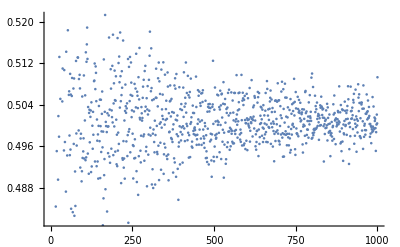

## Code

```mathematica
monteCarlo[h_]:=(counter = 0;
For[i=1,i≤h,i++,
chosenHand = RandomChoice[hand];
If[(pairRemoveSuiteQ[chosenHand]&&Not[pairWithFlushQ[chosenHand]]),counter++]
];
N[counter/h])

array=Range[1000];
(*Run monte carlo 1000 times*)
For[j=1, j<=1000,j++,
array[[j]] = monteCarlo[j^1.5];
];
array(*Print array*)
```

```mathematica
ListPlot[array]
```

-Graphics-